Effective hamiltonian (RWA)

(-ℏ Δ_p | -ℏ Ω_c | -ℏ Ω_p
-ℏ Conjugate[Ω_c] | -ℏ (-Δ_c+Δ_p) | 0
-ℏ Conjugate[Ω_p] | 0 | 0)

Density matrix

(ρ_(1,1) | ρ_(1,2) | ρ_(1,3)
ρ_(2,1) | ρ_(2,2) | ρ_(2,3)
ρ_(3,1) | ρ_(3,2) | ρ_(3,3))

Decay matrix

(-γ_(1,2) ρ_(1,1)-γ_(1,3) ρ_(1,1) | -1/2 γ_(1,2) ρ_(1,2)-1/2 γ_(1,3) ρ_(1,2) | -1/2 γ_(1,2) ρ_(1,3)-1/2 γ_(1,3) ρ_(1,3)
-1/2 γ_(1,2) ρ_(2,1)-1/2 γ_(1,3) ρ_(2,1) | γ_(1,2) ρ_(1,1) | 0
-1/2 γ_(1,2) ρ_(3,1)-1/2 γ_(1,3) ρ_(3,1) | 0 | γ_(1,3) ρ_(1,1))

Density matrix equations

Set::write: Tag Times in ( Augmented matrix  m1 MatrixForm)[«1»] is Protected.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[m1].

Set::write: Tag Times in m2 m1 is Protected.

CreateDirectory::privv: Privilege violation for file or directory C:\Users\nilam\.

Export::nodir: Directory C:\Users\nilam\Desktop\ does not exist.

OpenWrite::noopen: Cannot open C:\Users\nilam\Desktop\myfile5.dat.

Set::write: Tag Times in ( Augmented matrix  m1 MatrixForm)[«1»] is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

CreateDirectory::privv: Privilege violation for file or directory C:\Users\nilam\.

Export::nodir: Directory C:\Users\nilam\Desktop\ does not exist.

OpenWrite::noopen: Cannot open C:\Users\nilam\Desktop\myfile5.dat.

CreateDirectory::privv: Privilege violation for file or directory C:\Users\nilam\.

General::stop: Further output of CreateDirectory::privv will be suppressed during this calculation.

Export::nodir: Directory C:\Users\nilam\Desktop\ does not exist.

General::stop: Further output of Export::nodir will be suppressed during this calculation.

OpenWrite::noopen: Cannot open C:\Users\nilam\Desktop\myfile5.dat.

General::stop: Further output of OpenWrite::noopen will be suppressed during this calculation.

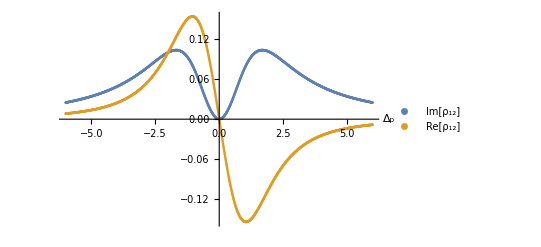

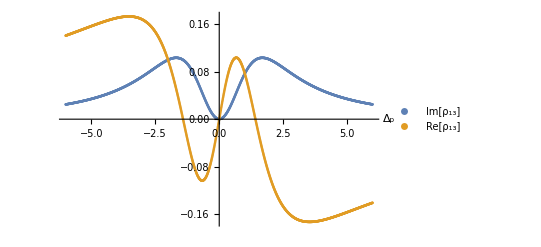

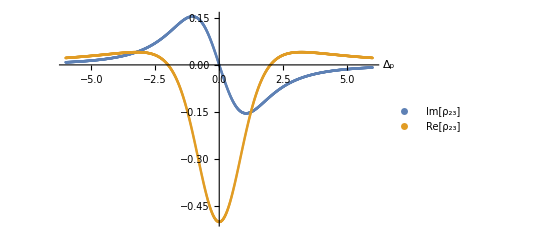

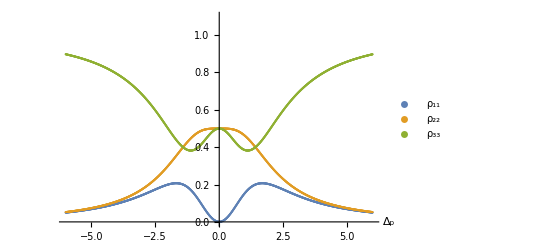

```mathematica
(* three level lambda system *)
(* |1> ----- Excited state *)
(* |2> ----- metastable state *)
(* |3> ----- ground state *)
(* Desnity matrix equations *)
Subscript[e, 1]=({{1}, {0}, {0}});
Subscript[e, 2]=({{0}, {1}, {0}});

Subscript[e, 3] =({{0}, {0}, {1}}) ;

"Effective hamiltonian (RWA)" 
Subscript[H, 3] = -ℏ*(Subscript[Ω, p]*Subscript[e, 1].Transpose[Subscript[e, 3]] + Subscript[Ω, c]*Subscript[e, 1].Transpose[Subscript[e, 2]] + Conjugate[Subscript[Ω, p]*Subscript[e, 3].Transpose[Subscript[e, 1]] + Subscript[Ω, c]*Subscript[e, 2].Transpose[Subscript[e, 1]]  ] +  Subscript[Δ, p]*Subscript[e, 1].Transpose[Subscript[e, 1]]+(Subscript[Δ, p]-Subscript[Δ, c])*Subscript[e, 2].Transpose[Subscript[e, 2]]  );
MatrixForm[Subscript[H, 3]]

" Density matrix "
rho = Table[Subscript[ρ, i,j],{i,3},{j,3}];
rho // MatrixForm

" Decay matrix "
For[i=1,i≤3,i++,
For[j=1,j≤3,j++,
Subscript[O, i,j]=Subscript[e, i].Transpose[Subscript[e, j]];
]]

For[i=1,i≤3,i++,
For[j=1,j≤3,j++,
Subscript[L, i,j] = (-Subscript[γ, i,j])/2*(Subscript[O, i,j].Subscript[O, j,i].rho +rho.Subscript[O, i,j].Subscript[O, j,i] -  2*Subscript[O, j,i].rho.Subscript[O, i,j]); 
]]

L = Subscript[L, 1,3]+Subscript[L, 1,2];
L//MatrixForm

" Density matrix equations "
X = -I*ℏ^-1*(Subscript[H, 3].rho - rho.Subscript[H, 3]) + L;
MatrixForm[FullSimplify[X,Assumptions->{t,ℏ,Subscript[Δ, p],Subscript[Δ, c],Subscript[γ, 1,3],Subscript[γ, 1,2],Subscript[γ, 2,3]}∈Reals]];


For[i=1,i≤3,i++,
For[j=1,j≤3,j++,
Subscript[f, i,j]=FullSimplify[Part[X,i,j],Assumptions->{t,ℏ,Subscript[Δ, p],Subscript[Δ, c],Subscript[γ, 1,3],Subscript[γ, 1,2],Subscript[γ, 2,3]}∈Reals];
]]


dataimagrho13=Array[1200,2];
datarealrho13=Array[1200,2];
Realrho13=Array[0,1200];
Imagrho13=Array[0,1200];

dataimagrho12=Array[1200,2];
datarealrho12=Array[1200,2];
Realrho12=Array[0,1200];
Imagrho12=Array[0,1200];

dataimagrho23=Array[1200,2];
datarealrho23=Array[1200,2];
Realrho23=Array[0,1200];
Imagrho23=Array[0,1200];

datarho11=Array[1200,2];
Rho11=Array[0,1200];
datarho22=Array[1200,2];
Rho22=Array[0,1200];
datarho33=Array[1200,2];
Rho33=Array[0,1200];


deltap=Array[0,1200];
For[k=1,k≤1200,k++,

Subscript[ρ, 1,1] := 1- Subscript[ρ, 2,2]- Subscript[ρ, 3,3]; 
Subscript[Δ, p]=-6 + (k-1)*0.01;
deltap[[k]]=Subscript[Δ, p];

Subscript[Δ, c]=0; 

Subscript[Ω, c]=1;
Subscript[Ω, p]=1;

Subscript[γ, 1,2] =1;Subscript[γ, 1,3]=1;

Subscript[γ, 2,3]=0.001;

eqns={Subscript[f, 1,2]==0,Subscript[f, 1,3]==0,Subscript[f, 2,1]==0,Subscript[f, 2,2]==0,Subscript[f, 2,3]-Subscript[γ, 2,3]*Subscript[ρ, 2,3]==0,Subscript[f, 3,1]==0,Subscript[f, 3,2]-Subscript[γ, 2,3]*Subscript[ρ, 3,2]==0,Subscript[f, 3,3]==0};

{b,m}=CoefficientArrays[eqns,{Subscript[ρ, 1,2],Subscript[ρ, 1,3],
Subscript[ρ, 2,1],Subscript[ρ, 2,2],Subscript[ρ, 2,3],
Subscript[ρ, 3,1],Subscript[ρ, 3,2],Subscript[ρ, 3,3]}];

" Constant matrix "
b //MatrixForm

" Coefficient matrix "
m // MatrixForm

" Augmented matrix "
m1 = MapThread[Append,{m,b}];
MatrixForm[m1]

(* write the augmented matrix to a file *)
m2=Partition[Map[FortranForm[#]&,Flatten[m1]],9];
Export["/Users/nilam/Desktop/myfile5.dat",m2,"Table"];


s1 = LinearSolve[m,-b];
Realrho12[[k]]=Re[s1[[1]]];
Imagrho12[[k]]=Im[s1[[1]]];

Realrho13[[k]]=Re[s1[[2]]];
Imagrho13[[k]]=Im[s1[[2]]];

Realrho23[[k]]=Re[s1[[5]]];
Imagrho23[[k]]=Im[s1[[5]]];

Rho22[[k]]=Abs[s1[[4]]];
Rho33[[k]]=Abs[s1[[8]]];
Rho11[[k]]=1 - Abs[s1[[4]]]-Abs[s1[[8]]];
]

datatoplot = {deltap,Imagrho12};
dataimagrho12 = Transpose[datatoplot];
datatoplot = {deltap,Realrho12};
datarealrho12 = Transpose[datatoplot];

ListPlot[{dataimagrho12,datarealrho12},PlotStyle->Thick,PlotLegends->{"Im[ρ_12]","Re[ρ_12]"}, Axes->True,AxesLabel->{"Δ_p"},PlotRange->All]
Clear[datatoplot,dataimagrho12,datarealrho12];

datatoplot = {deltap,Imagrho13};
dataimagrho13 = Transpose[datatoplot];
datatoplot = {deltap,Realrho13};
datarealrho13 = Transpose[datatoplot];

ListPlot[{dataimagrho13,datarealrho13},PlotStyle->Thick,PlotLegends->{"Im[ρ_13]","Re[ρ_13]"}, Axes->True,AxesLabel->{"Δ_p"},PlotRange->All]
Clear[datatoplot,dataimagrho13,datarealrho13]

datatoplot = {deltap,Imagrho23};
dataimagrho23 = Transpose[datatoplot];
datatoplot = {deltap,Realrho23};
datarealrho23 = Transpose[datatoplot];

ListPlot[{dataimagrho23,datarealrho23},PlotStyle->Thick,PlotLegends->{"Im[ρ_23]","Re[ρ_23]"}, Axes->True,AxesLabel->{"Δ_p"},PlotRange->All]
Clear[datatoplot,dataimagrho23,datarealrho23]

datatoplot = {deltap,Rho11};
datarho11 = Transpose[datatoplot];
datatoplot = {deltap,Rho22};
datarho22 = Transpose[datatoplot];
datatoplot = {deltap,Rho33};
datarho33 = Transpose[datatoplot];

ListPlot[{datarho11,datarho22,datarho33},PlotStyle->Thick,PlotLegends->{"ρ_11","ρ_22","ρ_33"}, Axes->True,AxesLabel->{"Δ_p"},PlotRange->{All,{0,1.1}}]
Clear[datatoplot,datarho11,datarho22,datarho33]


Subscript[Δ, p]=.;Subscript[Δ, c] =. ;Subscript[Ω, c]=.; Subscript[Ω, p]=.;
Subscript[ρ, 1,1]=.;
Subscript[γ, 1,3]=.;Subscript[γ, 1,2]=.; Subscript[γ, 2,3]=.;
```